```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2+z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2+z^2==-1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2-z^2==1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2-z^2==-1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot3D[x^2+y^2-z^2==a,{x,-2,2},{y,-2,2},{z,-2,2}]
,{a,-1,1}]
```

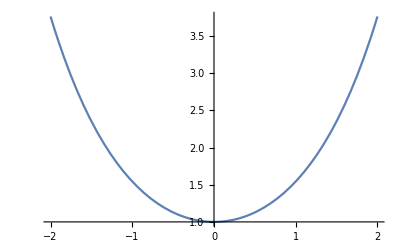

```mathematica
Plot[Cosh[x],{x,-2,2}]
```

```mathematica
Normalize[{1,1}].Normalize[{1,0}]
```

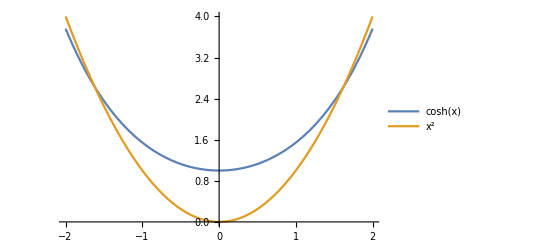

```mathematica
Plot[{Cosh[x],x^2},{x,-2,2},PlotLegends->"Expressions"]
```

```mathematica
Integrate[1/(√(1-x^4)),x]
```

EllipticF[ArcSin[x],-1]

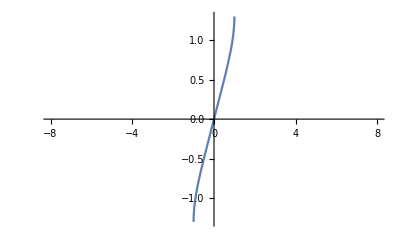

```mathematica
Plot[EllipticF[ArcSin[x],-1],{x,-8,8}]
```

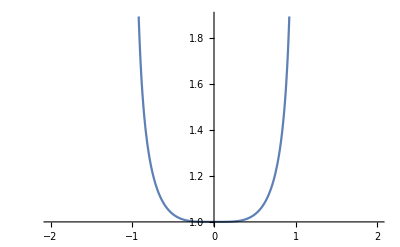

```mathematica
Plot[1/(√(1-x^4)),{x,-2,2}]
```

```mathematica
D[y[x,t],{x,-2}]==D[y[x,t],{t,2}]
```

D::dvar: Multiple derivative specifier {x,-2} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,-2} y[x,t]==y^(0,2)[x,t]

```mathematica
D[y[x,t],{x,2}]==D[y[x,t],{t,2}]
```

y^(2,0)[x,t]==y^(0,2)[x,t]

```mathematica
DSolve[Derivative[2,0][y][x,t]==Derivative[0,2][y][x,t],{y[x,t],y[x,t]},{t,x}]
```

{{y[x,t]→C[1][-t+x]+C[2][t+x]}}

```mathematica
Plot3D[Sin[π x] Cos[π t],{x,-2π,2π},{t,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[π x] Cos[π t],{x,-2π,2π},{t,0,3}]
```

-Graphics3D-

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
f[x]==x
```

f[x]==x

```mathematica
f[x]==x∧g[x]==x+ϵ
```

f[x]==x&&g[x]==x+ϵ

```mathematica
f[x]->g[x]
```

f[x]→g[x]

```mathematica
g[f[x]]->x
```

g[f[x]]→x

```mathematica
g[f[x]]->x
```

g[f[x]]→x

```mathematica
⋱[x,f[x]]==-1/f'[x]
```

⋱[x,f[x]]==-1/f'[x]

```mathematica
DSolve[⋱[x,f[x]]==-1/f'[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[⋱[x,f[x]]==-1/f'[x],{f[x]},{x}]

```mathematica
With[{f=Function[x, x x x]},
-1/f'[x]
]
```

-1/(3 x^2)

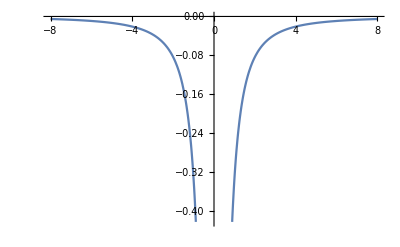

```mathematica
Plot[-1/(3 x^2),{x,-8,8}]
```

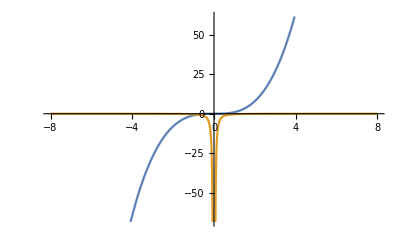

```mathematica
Plot[{x^3,-1/(3 x^2)},{x,-8,8}]
```

```mathematica
Plot[{x^3,-1/(3 x^2)},{x,-8,8}]
```

-Graphics-

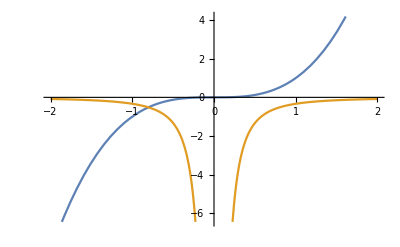

```mathematica
Plot[{x^3,-1/(3 x^2)},{x,-2,2}]
```

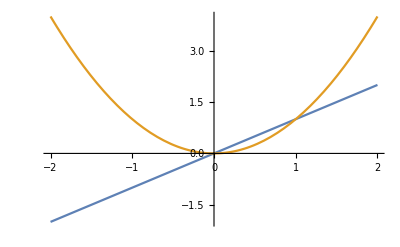

```mathematica
Plot[{x,x x},{x,-2,2}]
```

```mathematica
Manipulate[
Plot[{x,x x,(1-a)x+a x^2},{x,-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[{x,x x,(1-a)x+a x^2,x^2-x},{x,-2,2}]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[{x,x x,(1-a)x+a x^2,x^2-x},{x,-2,2}
,PlotLegends->"Expressions"]
,{a,0,1}]
```

```mathematica
Manipulate[
Plot[{x,x x,(1-a)x+a x^2,x^2-x},{x,-2,2}
,PlotLegends->"Expressions"]
,{a,0,1}]
```

```mathematica
EntityClass["PlaneCurve","Involute"]
```

involutes

```mathematica
EntityList[EntityClass["PlaneCurve","Involute"]]
```

{circle involute,ellipse involute,parabola involute}

```mathematica
Entity["PlaneCurve","ParabolaInvolute"]
```

parabola involute

```mathematica
PlaneCurveData[Entity["PlaneCurve","ParabolaInvolute"],"EvoluteName"]
```

Missing[UnknownProperty,{PlaneCurve,EvoluteName}]

```mathematica
PlaneCurveData[Entity["PlaneCurve","ParabolaInvolute"],"CartesianEquation"]
```

Missing[NotAvailable]

```mathematica
Solve[{f[x]==x,g[x]==-x,f[x]==g[x]},x]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -2 x == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
Solve[{f[x]==x,g[x]==-x},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f[x]==x,g[x]==-x},x]

```mathematica
y-Subscript[y, 1]==(x-Subscript[x, 1])m
```

y-y_1==m (x-x_1)

```mathematica
y=(x-α)m+f[α]
```

m (x-α)+f[α]

```mathematica
Manipulate[
Plot[{x^2,2x(x-a)+a a},{x,-2,2},PlotLegends->"Expressions"]
,{a,-2,2}]
```

```mathematica
Manipulate[
Plot[{x^2,2a(x-a)+a a},{x,-2,2},PlotLegends->"Expressions"]
,{a,-2,2}]
```

```mathematica
Manipulate[
Plot[
{x^2,2a(x-a)+a a}
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->{-1,4}]
,{a,-2,2}]
```

```mathematica
Manipulate[
Plot[
{x^2,2a(x-a)+a a,-(x-a)/(2a)+a a}
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->{-1,4}]
,{a,-2,2}]
```